# a composite image encryption algorithm using a 3-order cellular neural network and a symmetric-key block cipher

## Atriya Sen* and Syamal Kumar Dana**

* M. C. A. student
Pailan College of Management & Technology, Bengal Pailan Park, Kolkata - 700 104, India, Email: atriya.ind@gmail.com
** Head, Central Instrumentation Unit
Indian Institute of Chemical Biology, 4, Raja S. C. Mullick Road, Kolkata - 700 032, India, Email: skdana@iicb.res.in

## introduction and motivation

The idea of using chaos for encryption can be traced to Shannon, who suggested the use of measure-preserving transformations which depend on their arguments in a sensitive way.

The properties of sensitive dependence on initial conditions, ergocidy and mixing ensure that chaotic encryption systems satisfy the classic Shannon requirements of confusion and diffusion.

According to several authors, an extension of the domain of a classical encryption algorithm from a finite field to a continuum will give rise to a chaotic map. For example, the domain extension for the round function of the DES algorithm was proved to be a chaotic map. A fundamental relationship between chaos and cryptography is suspected.

Although algebraic cryptography algorithms such as DES can be applied to image cryptography, they are easily attacked because of their short encryption key. Public encryption algorithms can provide a long key, but are unsuitable for image encryption due to their slow speed. Also, established cryptanalytic techniques exist against these algorithms, such as linear and differential cryptanalysis.

Chaotic encryption schemes have traditionally used discrete-time chaotic systems, typically the logistic map. Also, [7] uses a feedback-enabled logistic map and [13] combines a logistic map with a cellular neural network. However, general methods of attack [11, 12] have been devised against such systems. Further, the design of the key space is flawed and it is difficult to estimate the security compared to conventional encryption schemes.

[14] concludes from statistical analysis that chaos is a necessary but not sufficient property of encryption algorithms and that the best results will be obtained by combining classical and chaotic cryptographic techniques. Along these lines, [15] suggests combining an elementary map with an XOR operation. It concludes that the resulting hybrid algorithm is highly resistant to a brute-force attack.

In light of all the above, an algorithm for image encryption adopting a 3-order cellular neural network as the chaotic signal generator, combined with the conventional encryption algorithm DES, is presented according the idea in [10].

◀     |     ▶

## the cellular neural network

A cellular neural network (CNN) is any spatial arrangement of numerous locally-coupled analog processing elements (cells), each of which has an input, an output and a state evolving according to some prescribed nonlinear dynamical laws. The resulting network is defined mathematically by four specifications: the cell dynamics, boundary conditions and initial conditions, and a synaptic law.

The cell dynamics of the original Chua-Yang CNN model [6] is governed by the state equations:

(ẋ)_(i,j)=-x_(i,j)+a_(0,0)y_(i,j)+b_(0,0)u_(i,j)+z+I_(i,j)^s
						y_(i,j)=f(x_(i,j))=1/2(|x_(i,j)+1|-|x_(i,j)-1|),

where x_(i,j),y_(i,j),u_(i,j),z,I_(i,j)^s∈ℝ (first order cells).

The synaptic law is given by:

I_(i,j)^s=∑_(k,l∈S_(i,j)) a_(k-i,l-j)y_(k,l)+b_(k-i,l-j)u_(k,l)

A fixed boundary condition was proposed in [6]: the CNN be clamped at its ends to value 0. However, other boundary conditions can be used as well.

CNNs perform parallel processing to solve given computational tasks, such as processing and also producing information signals. The local interconnections make CNN models tailor-made for monolithic implementation in currently available planar technologies, such as VLSI. The CNN universal machine (CNN-UM) was the first algorithmically programmable (Turing-complete) analogic microprocessor, combining analog array computing with logic operations. Applications include image-processing and the generation of chaotic and hyper-chaotic signals.

◀     |     ▶

## dynamics of the 3-order CNN

The simplest CNN model exhibiting chaotic phenomena, a 3-order CNN dynamic model with full-connecting [9] was selected:

OverDot[x_i]=-x_i+a_i y_i+∑_(k=1,k≠i)^3 a_ik y_i+∑_(k=1)^3 s_ik x_k+I_i, i=1,2,3,

where x_i is the state variable of cell i and y_i denotes the output of cell i, defined as:

y_i=0.5(|x_i+1|-|x_i-1|), i=1,2,3

Selected cell template parameters:

a_12=a_13=a_2=a_23=a_32=a_3=a_21=a_31=0
					s_13=s_31=s_22=I_1=I_2=I_3=0
					s_21=s_23=s_33=1

Then, we get from (3):

OverDot[x_1]=a_1 y_1+s_11 x_1+s_12 x_2-x_1
					OverDot[x_2]=x_1-x_2+x_3
					OverDot[x_3]=s_32 x_2

And from (4):

y_1=0.5(|x_1+1|-|x_1-1|)

So:

```mathematica
CNNvars={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t]};

CNNf=-Subscript[x, 1][t]+Subscript[a, 1]*5/10*(Abs[Subscript[x, 1][t]+1]-Abs[Subscript[x, 1][t]-1])+Subscript[s, 11] Subscript[x, 1][t]+Subscript[s, 12] Subscript[x, 2][t];
CNNg=-Subscript[x, 2][t]+Subscript[x, 1][t]+Subscript[x, 3][t];
CNNh=Subscript[s, 32] Subscript[x, 2][t];

CNNeqns={Subscript[x, 1]'[t]==CNNf,Subscript[x, 2]'[t]==CNNg,Subscript[x, 3]'[t]==CNNh};
```

It was proved that for all s_11<2 (when |x_1|>1) and for all a_1+s_11<2 (when |x_1|⩽1), the system is dissipative, with an exponential contraction rate e^(s_11-2) and e^(a_1+s_11-2) respectively. The system orbits are ultimately confined into a specific limit set of zero volume, and the system asymptotic motion settles onto an attractor.

Selecting the parameters a_1=3.86,s_11=-1.55,s_12=8.98,s_32=-14.26 and the initial condition x(0)=[0.2,0.2,0.2], pairwise plane trajectories were plotted:

```mathematica
CNNinits={Subscript[x, 1][0]==2/10,Subscript[x, 2][0]==2/10,Subscript[x, 3][0]==2/10};

Subscript[a, 1]=386/100;Subscript[s, 11]=-155/100;Subscript[s, 12]=898/100;Subscript[s, 32]=-1426/100;

sol1=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,0,50}]⟦1⟧;
sol2=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,0,50},WorkingPrecision->25,PrecisionGoal->12,AccuracyGoal->12]⟦1⟧;
sol3={sx,sy,sz}=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,0,50},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->14000]⟦1⟧;
sol4=CNNvars/.NDSolve[Join[CNNeqns,{Subscript[x, 1][0]==2001/10000,Subscript[x, 2][0]==2/10,Subscript[x, 3][0]==2/10}],CNNvars,{t,0,40},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->13000]⟦1⟧;
```

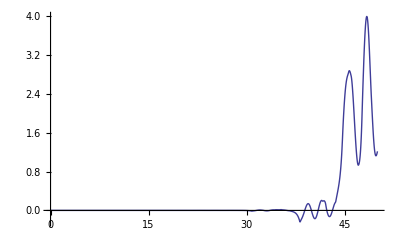
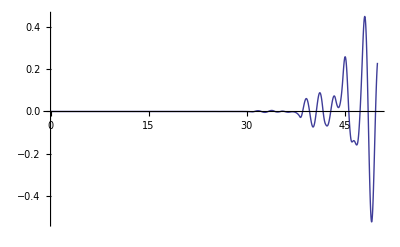
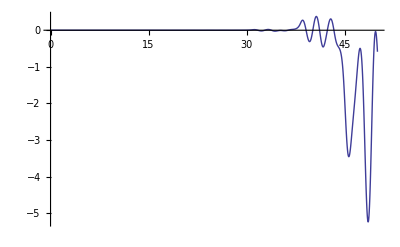

```mathematica
Plot[#,{t,0,50},PlotRange->All]&/@(sol1-sol2)
```

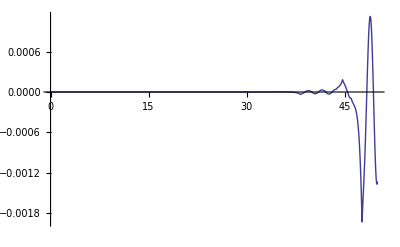
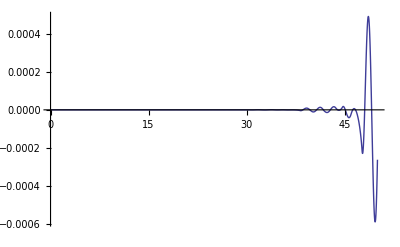
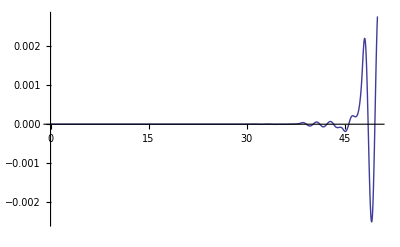

```mathematica
Plot[#,{t,0,50},PlotRange->All]&/@(sol2-sol3)
```

This sensitivity makes the prediction of a chaotic system impossible after a certain point, due to limited computational precision.

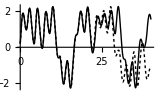

```mathematica
Plot[Evaluate[{sol3⟦1⟧,sol4⟦1⟧}],{t,0,40},PlotStyle->{{Black,Dashing[{Tiny}]},{Black}},ImageSize->160]
```

This sensitivity makes the prediction of a chaotic system impossible after a certain point, since the initial conditions are hardly known exactly.

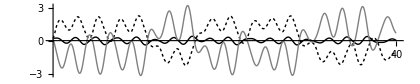

```mathematica
Plot[sol3,{t,0,40},Ticks->{{40},Automatic},PlotStyle->{{Black,Dashing[{Tiny}]},{Black},{Gray}},ImageSize->420,AspectRatio->0.2]
```

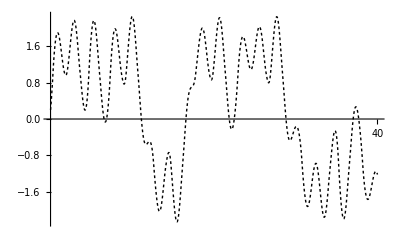
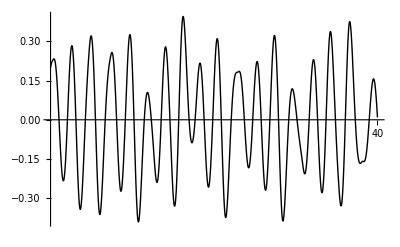
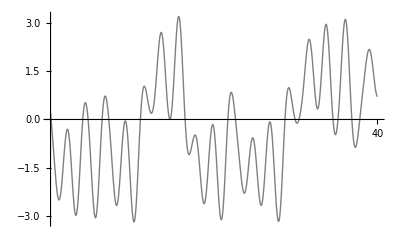

```mathematica
MapThread[Plot[#1,{t,0,40},PlotStyle->#2,Ticks->{{40},Automatic}]&,{sol3,{{Black,Dashing[{Tiny}]},{Black},{Gray}}}]
```

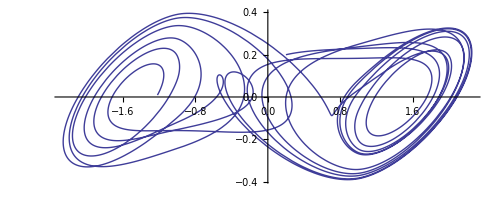
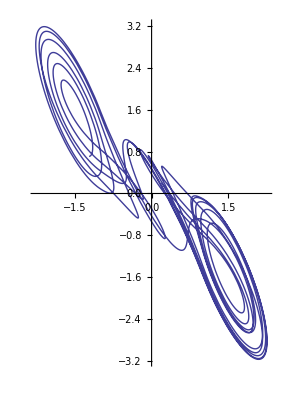
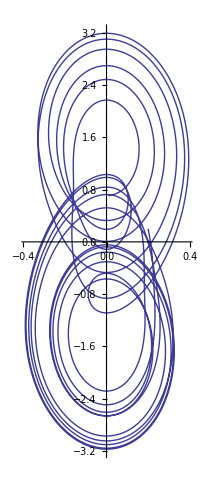

```mathematica
ParametricPlot[#,{t,0,40}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

Selecting different parameters, different characteristic chaotic attractors were gained:

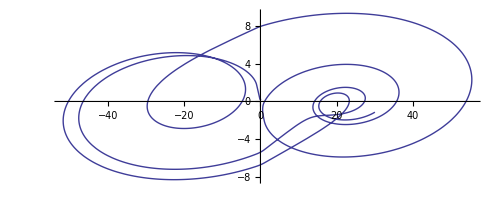
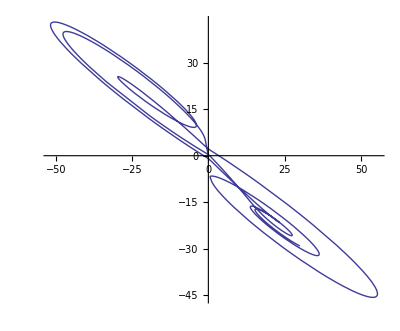
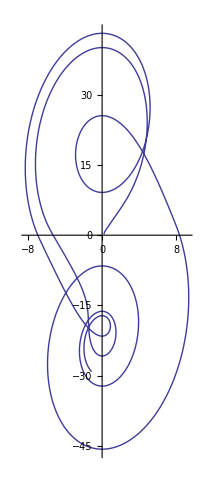

```mathematica
Subscript[a, 1]=-7717/1000;Subscript[s, 11]=13443/10000;Subscript[s, 12]=-4925/1000;Subscript[s, 32]=3649/1000;
sol3b={sx,sy,sz}=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,0,50},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->14000]⟦1⟧;
ParametricPlot[#,{t,0,40}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

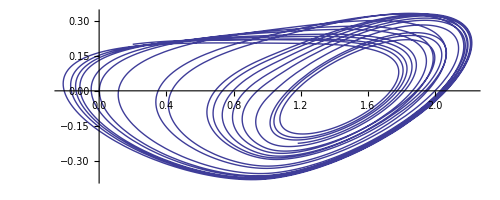
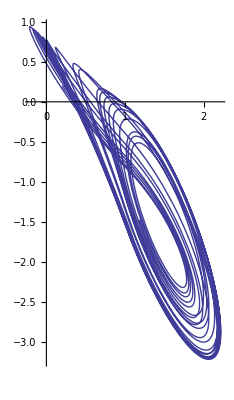
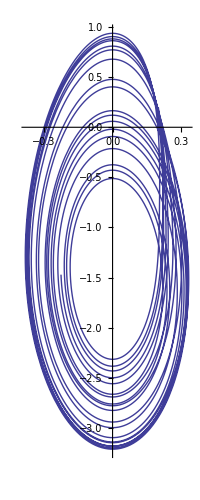

```mathematica
Subscript[a, 1]=40279/10000;Subscript[s, 11]=-16856/10000;Subscript[s, 12]=94/10;Subscript[s, 32]=-16;
sol3c={sx,sy,sz}=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,0,50},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->14000]⟦1⟧;
ParametricPlot[#,{t,0,40}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

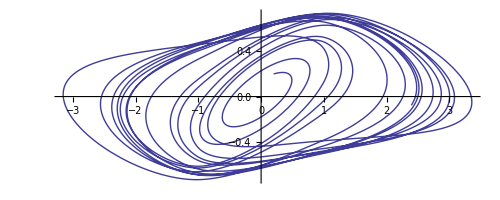
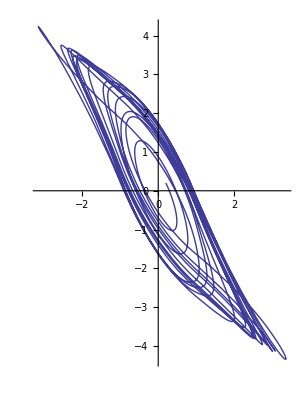
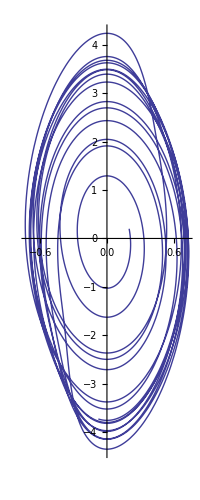

```mathematica
Subscript[a, 1]=-36805/10000;Subscript[s, 11]=22179/10000;Subscript[s, 12]=8342/1000;Subscript[s, 32]=-11925/1000;
sol3d={sx,sy,sz}=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,0,50},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->14000]⟦1⟧;
ParametricPlot[#,{t,0,40}]&/@{{sx,sy},{sx,sz},{sy,sz}}
```

◀     |     ▶

## algorithm

-Graphics-

c=p⊕x,

where x_j=round(K √(x_(1j)^2+x_(2j)^2+x_(3j)^2)+λ)  mod 256, where x_(1j), x_(2j) and x_(3j) are the numerical solutions of state variables in equation (6) on time j; x is composed of x_(j mod A+40); the constants K, λ and A are control parameters.

d=DES_k(c),

where k is the 64-bit DES key.

Transmission over a possibly noisy insecure channel gives d̂.

ĉ=DES_(k̂)^-1(d̂),

where k̂=k; the function DES^-1 represents DES decryption.

p̂=x̂⊕ĉ,

where x̂=x.

Summarily,

p̂=x̂⊕DES_(k̂)^-1[DES_k(p⊕x)]

### notes

The chaotic signals used in the CNN-encryption are obtained after rounding, taking modulus, squaring, evolution, magnification and excursion, and are different from the original chaotic sequences. Confusion is increased because of the complex calculation involved and the parameters.

A determines the number of pseudo-random values used in CNN-encryption (and CNN-decryption). It is a measure of the robustness of the cipher-image, and may be increased (up to the total number of pixels in the plain-image), at the cost of computational expense.

Pseudo random values at t<41 were not used, since it was determined that these values are comparatively less sensitive to changes in computational precision.

◀     |     ▶

## simulation results

The scheme was simulated in Mathematica 7 with internal precision = 25, K=3000, λ=127, A=256 and the DES key "3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&3#.)+w*&".

### declarations

```mathematica
DESkey=Import["C:\\Users\\Atriya\\Documents\\key.txt","Byte"];
```

Chosen plain-image:

```mathematica
image=-Graphics-;
cols=ImageDimensions[image]⟦1⟧;
```

```mathematica
CNNvars={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t]};

CNNf=-Subscript[x, 1][t]+Subscript[a, 1]*5/10*(Abs[Subscript[x, 1][t]+1]-Abs[Subscript[x, 1][t]-1])+Subscript[s, 11] Subscript[x, 1][t]+Subscript[s, 12] Subscript[x, 2][t];
CNNg=-Subscript[x, 2][t]+Subscript[x, 1][t]+Subscript[x, 3][t];
CNNh=Subscript[s, 32] Subscript[x, 2][t];

CNNeqns={Subscript[x, 1]'[t]==CNNf,Subscript[x, 2]'[t]==CNNg,Subscript[x, 3]'[t]==CNNh};
CNNinits={Subscript[x, 1][0]==2/10,Subscript[x, 2][0]==2/10,Subscript[x, 3][0]==2/10};
Subscript[a, 1]=386/100;Subscript[s, 11]=-155/100;Subscript[s, 12]=898/100;Subscript[s, 32]=-1426/100;
CNNK=3000;CNNλ=127;CNNA=256;

CNNsol3=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,41,CNNA+40},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->1000000]⟦1⟧;
CNNsol4=CNNvars/.NDSolve[Join[CNNeqns,{Subscript[x, 1][0]==2001/10000,Subscript[x, 2][0]==2/10,Subscript[x, 3][0]==2/10}],CNNvars,{t,0,CNNA+40},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->1000000]⟦1⟧;
CNNsol5=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,0,CNNA+40},WorkingPrecision->24,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->1000000]⟦1⟧;

CNNvals={};
Do [
AppendTo[CNNvals,CNNsol3/.t->(i+40)],
{i,CNNA}
]
CNNvals2={};
Do [
AppendTo[CNNvals2,CNNsol4/.t->(i+40)],
{i,CNNA}
]
CNNvals3={};
Do [
AppendTo[CNNvals3,CNNsol5/.t->(i+40)],
{i,CNNA}
]
```

### CNN encryption

#### encryption

```mathematica
plainbytes=Flatten[ImageData[image,"Byte"]];
```

```mathematica
CNNcipherbytes={};
Do [
r=Mod[Round[CNNK√((CNNvals⟦Mod[i,CNNA]+1,1⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,2⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,3⟧)^2)+CNNλ],256];
AppendTo[CNNcipherbytes,BitXor[plainbytes⟦i⟧,r]],
{i,Length[plainbytes]}
]
```

#### bytes -> bits

```mathematica
temp={};
Do [
AppendTo[temp,IntegerDigits[CNNcipherbytes⟦i⟧,2,8]],
{i,Length[CNNcipherbytes]}
]
```

```mathematica
CNNcipherbits=Flatten[temp];
```

### DES encryption

```mathematica
prepared=Partition[CNNcipherbits,64,64,1,0];
```

```mathematica
processed={};
Do [
AppendTo[processed,DESEncrypt[prepared⟦i⟧,DESkey]],
{i,Length[prepared]}
]
```

```mathematica
DEScipherbits=Flatten[processed];
Export["C:\\Users\\Atriya\\Documents\\DEScipherbits.txt",DEScipherbits,"Bit"];
```

### encrypted image reconstruction

```mathematica
temp=Partition[DEScipherbits,8];
```

```mathematica
DEScipherbytes={};
Do [
AppendTo[DEScipherbytes,FromDigits[temp⟦i⟧,2]],
{i,Length[temp]}
]
```

Obtained cipher-image:

```mathematica
Image[Partition[Partition[DEScipherbytes,3],cols],"Byte"]
```

-Graphics-

### DES decryption

```mathematica
prepared=Partition[DEScipherbits,64,64,1,0];
```

```mathematica
processed={};
Do [
AppendTo[processed,DESDecrypt[prepared⟦i⟧,DESkey]],
{i,Length[prepared]}
]
```

```mathematica
DESdecipherbits=Flatten[processed];
```

### CNN decryption

#### bits -> bytes

```mathematica
temp=Partition[DESdecipherbits,8];
```

```mathematica
DESdecipherbytes={};
Do [
AppendTo[DESdecipherbytes,FromDigits[temp⟦i⟧,2]],
{i,Length[temp]}
]
```

#### decryption

Image recovered after decryption (assuming perfect transmission):

```mathematica
CNNdecipherbytes={};
Do [
r=Mod[Round[CNNK√((CNNvals⟦Mod[i,CNNA]+1,1⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,2⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,3⟧)^2)+CNNλ],256];
AppendTo[CNNdecipherbytes,BitXor[r,DESdecipherbytes⟦i⟧]],
{i,Length[DESdecipherbytes]}
]
```

```mathematica
Image[Partition[Partition[CNNdecipherbytes,3],cols],"Byte"]
```

-Graphics-

### correctness test

A bytewise comparison of the original and decrypted images is performed:

```mathematica
donebytes=Flatten[ImageData[-Graphics-,"Byte"]];
```

```mathematica
plainbytes==donebytes
```

True

### incorrect decryption

Recovered image using the (slightly) incorrect x(0)=[0.2001,0.2,0.2]:

```mathematica
CNNdecipherbytes2={};
Do [
r=Mod[Round[CNNK√((CNNvals2⟦Mod[i,CNNA]+1,1⟧)^2+(CNNvals2⟦Mod[i,CNNA]+1,2⟧)^2+(CNNvals2⟦Mod[i,CNNA]+1,3⟧)^2)+CNNλ],256];
AppendTo[CNNdecipherbytes2,BitXor[r,DESdecipherbytes⟦i⟧]],
{i,Length[DESdecipherbytes]}
]
```

```mathematica
Image[Partition[Partition[CNNdecipherbytes2,3],cols],"Byte"]
```

-Graphics-

Recovered image using the (slightly) incorrect internal precision of 24:

```mathematica
CNNdecipherbytes3={};
Do [
r=Mod[Round[CNNK√((CNNvals3⟦Mod[i,CNNA]+1,1⟧)^2+(CNNvals3⟦Mod[i,CNNA]+1,2⟧)^2+(CNNvals3⟦Mod[i,CNNA]+1,3⟧)^2)+CNNλ],256];
AppendTo[CNNdecipherbytes3,BitXor[r,DESdecipherbytes⟦i⟧]],
{i,Length[DESdecipherbytes]}
]
```

```mathematica
Image[Partition[Partition[CNNdecipherbytes3,3],cols],"Byte"]
```

-Graphics-

◀     |     ▶

## simulation of imperfect transmission

Imperfect transmission is simulated by substituting a random bit value at randomly selected locations in the transmitted bitstream. Images recovered after decryption are shown against the corresponding imperfection factors (fraction of 'bad' bits in the bitstream):

```mathematica
data={};
pics={};
badblocksize=256;
Do [
DEScipherbits=Import["C:\\Users\\Atriya\\Documents\\DEScipherbits.txt","Bit"];
l=Length[DEScipherbits];
noisefactor=j;
badbits=l*noisefactor;
banned={};
Do [
mybit=RandomInteger[{1,l-badblocksize}];
While [MemberQ[banned,mybit],
mybit=RandomInteger[{1,l-badblocksize}]
];
AppendTo[banned,Range[mybit,mybit+badblocksize-1]];
banned=Flatten[banned];
Do [
DEScipherbits⟦mybit+k⟧=RandomInteger[],
{k,badblocksize}
],
{i,badbits/badblocksize}
];
prepared=Partition[DEScipherbits,64,64,1,0];
processed={};
Do [
AppendTo[processed,DESDecrypt[prepared⟦i⟧,DESkey]],
{i,Length[prepared]}
];
DESdecipherbits=Flatten[processed];
temp=Partition[DESdecipherbits,8];
DESdecipherbytes={};
Do [
AppendTo[DESdecipherbytes,FromDigits[temp⟦i⟧,2]],
{i,Length[temp]}
];
CNNdecipherbytes={};
Do [
r=Mod[Round[CNNK√((CNNvals⟦Mod[i,CNNA]+1,1⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,2⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,3⟧)^2)+CNNλ],256];
AppendTo[CNNdecipherbytes,BitXor[r,DESdecipherbytes⟦i⟧]],
{i,Length[DESdecipherbytes]}
];
image2=Image[Partition[Partition[CNNdecipherbytes,3],cols],"Byte"];
one=Flatten[ImageData[image,"Byte"],1];
two=Flatten[ImageData[image2,"Byte"],1];
counter=0;
Do [
counter+=If [one⟦i⟧==two⟦i⟧,0,1],
{i,Length[one]}
];
AppendTo[data,{j,counter/Length[one]//N}];
AppendTo[pics,{j,image2}],
{j,{0.002,0.004,0.006,0.008,0.010,0.015,0.020,0.025,0.030,0.040,0.050,0.060,0.070,0.080,0.090,0.100}}
]
```

```mathematica
data1
```

{{0.002,0.0730218},{0.004,0.141371},{0.006,0.216947},{0.008,0.270654},{0.01,0.32},{0.015,0.436386},{0.02,0.534579},{0.025,0.607103},{0.03,0.680997},{0.04,0.774766},{0.05,0.841931},{0.06,0.886978},{0.07,0.918442},{0.08,0.942928},{0.09,0.95838},{0.1,0.97271}}

```mathematica
data8
```

{{0.002,0.0221184},{0.004,0.0405607},{0.006,0.0621807},{0.008,0.0819938},{0.01,0.100436},{0.015,0.147227},{0.02,0.189283},{0.025,0.229969},{0.03,0.26866},{0.04,0.343925},{0.05,0.406791},{0.06,0.474517},{0.07,0.525047},{0.08,0.568224},{0.09,0.609097},{0.1,0.648536}}

```mathematica
data16
```

{{0.002,0.0115265},{0.004,0.022866},{0.006,0.0344548},{0.008,0.0445483},{0.01,0.057134},{0.015,0.0805607},{0.02,0.108723},{0.025,0.131963},{0.03,0.160748},{0.04,0.211589},{0.05,0.251651},{0.06,0.301682},{0.07,0.337445},{0.08,0.375576},{0.09,0.410717},{0.1,0.453894}}

```mathematica
data32
```

{{0.002,0.00629283},{0.004,0.0138941},{0.006,0.0204361},{0.008,0.0272274},{0.01,0.0328972},{0.015,0.0471651},{0.02,0.0656075},{0.025,0.0842368},{0.03,0.097134},{0.04,0.131589},{0.05,0.160872},{0.06,0.191402},{0.07,0.222243},{0.08,0.242804},{0.09,0.269159},{0.1,0.295639}}

```mathematica
data64
```

{{0.002,0.00448598},{0.004,0.00897196},{0.006,0.0127726},{0.008,0.0167601},{0.01,0.0209969},{0.015,0.0323988},{0.02,0.0432399},{0.025,0.0531464},{0.03,0.0645483},{0.04,0.0864174},{0.05,0.105234},{0.06,0.125047},{0.07,0.144798},{0.08,0.166542},{0.09,0.184548},{0.1,0.202679}}

```mathematica
data128
```

{{0.002,0.00330218},{0.004,0.00654206},{0.006,0.00978193},{0.008,0.0132087},{0.01,0.0158879},{0.015,0.0237383},{0.02,0.0319003},{0.025,0.0398131},{0.03,0.0476636},{0.04,0.062866},{0.05,0.077757},{0.06,0.0917134},{0.07,0.108972},{0.08,0.123738},{0.09,0.138193},{0.1,0.151963}}

```mathematica
data256
```

{{0.002,0.00261682},{0.004,0.00523364},{0.006,0.00785047},{0.008,0.0104673},{0.01,0.0125857},{0.015,0.01919},{0.02,0.0250467},{0.025,0.0314642},{0.03,0.0390654},{0.04,0.0516511},{0.05,0.0628037},{0.06,0.0755763},{0.07,0.0889097},{0.08,0.100436},{0.09,0.112835},{0.1,0.123427}}

```mathematica
pics1
```

{{0.002,-Graphics-},{0.004,-Graphics-},{0.006,-Graphics-},{0.008,-Graphics-},{0.01,-Graphics-},{0.015,-Graphics-},{0.02,-Graphics-},{0.025,-Graphics-},{0.03,-Graphics-},{0.04,-Graphics-},{0.05,-Graphics-},{0.06,-Graphics-},{0.07,-Graphics-},{0.08,-Graphics-},{0.09,-Graphics-},{0.1,-Graphics-}}

```mathematica
pics8
```

{{0.002,-Graphics-},{0.004,-Graphics-},{0.006,-Graphics-},{0.008,-Graphics-},{0.01,-Graphics-},{0.015,-Graphics-},{0.02,-Graphics-},{0.025,-Graphics-},{0.03,-Graphics-},{0.04,-Graphics-},{0.05,-Graphics-},{0.06,-Graphics-},{0.07,-Graphics-},{0.08,-Graphics-},{0.09,-Graphics-},{0.1,-Graphics-}}

```mathematica
pics16
```

{{0.002,-Graphics-},{0.004,-Graphics-},{0.006,-Graphics-},{0.008,-Graphics-},{0.01,-Graphics-},{0.015,-Graphics-},{0.02,-Graphics-},{0.025,-Graphics-},{0.03,-Graphics-},{0.04,-Graphics-},{0.05,-Graphics-},{0.06,-Graphics-},{0.07,-Graphics-},{0.08,-Graphics-},{0.09,-Graphics-},{0.1,-Graphics-}}

```mathematica
pics32
```

{{0.002,-Graphics-},{0.004,-Graphics-},{0.006,-Graphics-},{0.008,-Graphics-},{0.01,-Graphics-},{0.015,-Graphics-},{0.02,-Graphics-},{0.025,-Graphics-},{0.03,-Graphics-},{0.04,-Graphics-},{0.05,-Graphics-},{0.06,-Graphics-},{0.07,-Graphics-},{0.08,-Graphics-},{0.09,-Graphics-},{0.1,-Graphics-}}

```mathematica
pics64
```

{{0.002,-Graphics-},{0.004,-Graphics-},{0.006,-Graphics-},{0.008,-Graphics-},{0.01,-Graphics-},{0.015,-Graphics-},{0.02,-Graphics-},{0.025,-Graphics-},{0.03,-Graphics-},{0.04,-Graphics-},{0.05,-Graphics-},{0.06,-Graphics-},{0.07,-Graphics-},{0.08,-Graphics-},{0.09,-Graphics-},{0.1,-Graphics-}}

```mathematica
pics128
```

{{0.002,-Graphics-},{0.004,-Graphics-},{0.006,-Graphics-},{0.008,-Graphics-},{0.01,-Graphics-},{0.015,-Graphics-},{0.02,-Graphics-},{0.025,-Graphics-},{0.03,-Graphics-},{0.04,-Graphics-},{0.05,-Graphics-},{0.06,-Graphics-},{0.07,-Graphics-},{0.08,-Graphics-},{0.09,-Graphics-},{0.1,-Graphics-}}

```mathematica
pics256
```

{{0.002,-Graphics-},{0.004,-Graphics-},{0.006,-Graphics-},{0.008,-Graphics-},{0.01,-Graphics-},{0.015,-Graphics-},{0.02,-Graphics-},{0.025,-Graphics-},{0.03,-Graphics-},{0.04,-Graphics-},{0.05,-Graphics-},{0.06,-Graphics-},{0.07,-Graphics-},{0.08,-Graphics-},{0.09,-Graphics-},{0.1,-Graphics-}}

Defining the distortion factor to be the fraction of 'bad' pixels in the recovered image, the following plots are obtained:

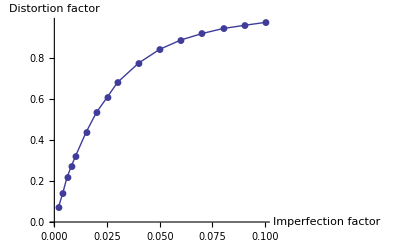

```mathematica
ListLinePlot[data1,AxesLabel->{"Imperfection factor","Distortion factor"},PlotMarkers->Automatic]
```

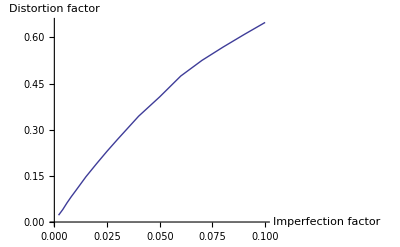

```mathematica
ListLinePlot[data8,AxesLabel->{"Imperfection factor","Distortion factor"}]
```

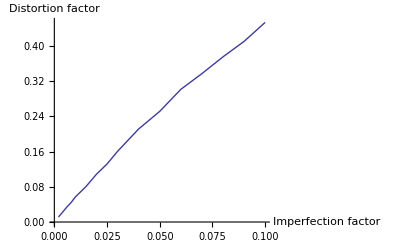

```mathematica
ListLinePlot[data16,AxesLabel->{"Imperfection factor","Distortion factor"}]
```

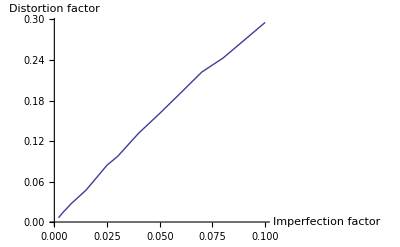

```mathematica
ListLinePlot[data32,AxesLabel->{"Imperfection factor","Distortion factor"}]
```

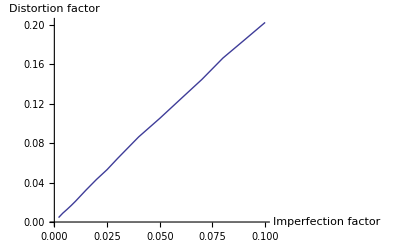

```mathematica
ListLinePlot[data64,AxesLabel->{"Imperfection factor","Distortion factor"}]
```

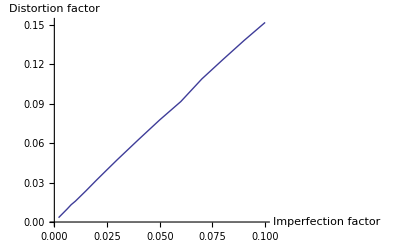

```mathematica
ListLinePlot[data128,AxesLabel->{"Imperfection factor","Distortion factor"}]
```

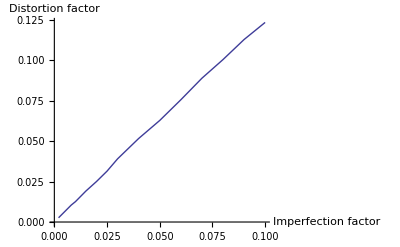

```mathematica
ListLinePlot[data256,AxesLabel->{"Imperfection factor","Distortion factor"}]
```

So, when bit substitution locations are clustered, recovery is found to be much more efficient.

The following plot is obtained for 1-bit (filled circle), 8-bit (filled square), 16-bit (filled diamond), 32-bit (filled triangle), 64-bit (filled inverted triangle), 128-bit (hollow circle) and 256-bit (hollow square) clusters:

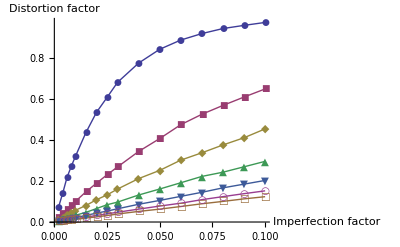

```mathematica
ListLinePlot[{data1,data8,data16,data32,data64,data128,data256},AxesLabel->{"Imperfection factor","Distortion factor"},PlotMarkers->Automatic]
```

◀     |     ▶

## statistical analysis

Shannon showed that many encryption schemes are vulnerable to statistical analysis. He proposed that such attacks could be resisted by improving confusion and diffusion, such that the cipher-image bears little or no statistical resemblance to the plain-image.

Obtained histogram of the plain-image:

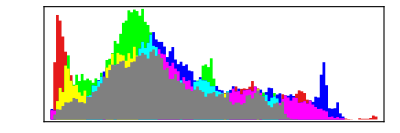

```mathematica
ImageHistogram[image]
```

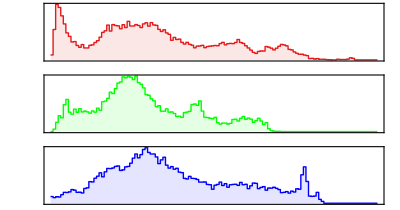

```mathematica
ImageHistogram[image,Appearance->"Separated"]
```

Obtained histogram of the cipher-image:

```mathematica
image2=-Graphics-;
```

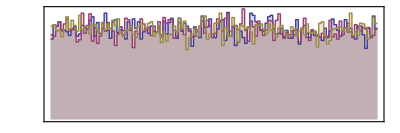

```mathematica
ImageHistogram[image2]
```

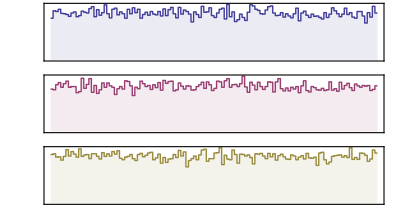

```mathematica
ImageHistogram[image2,Appearance->"Separated"]
```

The feature of equality observed in the cipher-image histogram signifies high confusion and diffusion. The magnitude of the peaks is much lesser in the cipher-image histogram, which is drawn to a much larger scale. Shown to scale, they would be no more than a low level of noise compared to the plain-image histogram peaks.

◀     |     ▶

## complexity analysis

### combined

```mathematica
data={};
Do [
image=ImageResize[-Graphics-,{j,3/4*j}];
pixels=ImageDimensions[image]⟦1⟧*ImageDimensions[image]⟦2⟧;
AppendTo[data,
{Timing [
CNNsol3=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,41,CNNA+40},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->45000]⟦1⟧;
CNNvals={};
Do [
AppendTo[CNNvals,CNNsol3/.t->(i+40)],
{i,CNNA}
];
plainbytes=Flatten[ImageData[image,"Byte"]];
CNNcipherbytes={};
Do [
r=Mod[Round[CNNK√((CNNvals⟦Mod[i,CNNA]+1,1⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,2⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,3⟧)^2)+CNNλ],256];
AppendTo[CNNcipherbytes,BitXor[plainbytes⟦i⟧,r]],
{i,Length[plainbytes]}
];
temp={};
Do [
AppendTo[temp,IntegerDigits[CNNcipherbytes⟦i⟧,2,8]],
{i,Length[CNNcipherbytes]}
];
CNNcipherbits=Flatten[temp];
prepared=Partition[CNNcipherbits,64,64,1,0];
processed={};
Do [
AppendTo[processed,DESEncrypt[prepared⟦i⟧,DESkey]],
{i,Length[prepared]}
];
DEScipherbits=Flatten[processed];
]⟦1⟧,pixels}
],
{j,{50,100,150,200,250,300}}
]
```

```mathematica
data
```

{{34.211,1900},{55.24,7500},{142.881,16950},{417.662,30000},{1112.15,47000},{2726.74,67500}}

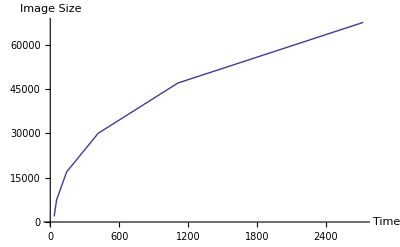

```mathematica
ListLinePlot[data,AxesLabel->{"Time","Image Size"}]
```

### separate

```mathematica
Do [
image=ImageResize[-Graphics-,{j,3/4*j}];
pixels=ImageDimensions[image]⟦1⟧*ImageDimensions[image]⟦2⟧;
plainbytes=Flatten[ImageData[image,"Byte"]];
CNNvals={};
CNNcipherbytes={};
AppendTo[dataCNN,
{Timing [
CNNsol3=CNNvars/.NDSolve[Join[CNNeqns,CNNinits],CNNvars,{t,41,CNNA+40},WorkingPrecision->25,PrecisionGoal->16,AccuracyGoal->16,MaxSteps->45000]⟦1⟧;
Do [
AppendTo[CNNvals,CNNsol3/.t->(i+40)],
{i,CNNA}
];
Do [
r=Mod[Round[CNNK√((CNNvals⟦Mod[i,CNNA]+1,1⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,2⟧)^2+(CNNvals⟦Mod[i,CNNA]+1,3⟧)^2)+CNNλ],256];
AppendTo[CNNcipherbytes,BitXor[plainbytes⟦i⟧,r]],
{i,Length[plainbytes]}
];
]⟦1⟧,pixels}
];
temp={};
Do [
AppendTo[temp,IntegerDigits[CNNcipherbytes⟦i⟧,2,8]],
{i,Length[CNNcipherbytes]}
];
CNNcipherbits=Flatten[temp];
prepared=Partition[CNNcipherbits,64,64,1,0];
processed={};
AppendTo[dataDES,
{Timing[
Do [
AppendTo[processed,DESEncrypt[prepared⟦i⟧,DESkey]],
{i,Length[prepared]}
];
]⟦1⟧,pixels}
];
DEScipherbits=Flatten[processed],
{j,{300}}
]
```

```mathematica
dataCNN
```

{{32.994,1900},{35.007,7500},{45.1,16950},{69.264,30000},{125.019,47000},{241.318,67500}}

```mathematica
dataDES
```

{{5.304,1900},{20.904,7500},{47.752,16950},{86.331,30000},{138.466,47000},{206.514,67500}}

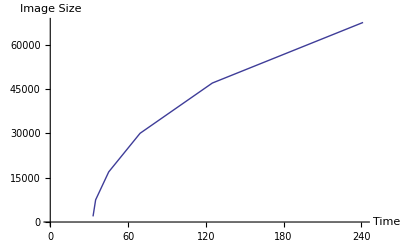

```mathematica
ListLinePlot[dataCNN,AxesLabel->{"Time","Image Size"}]
```

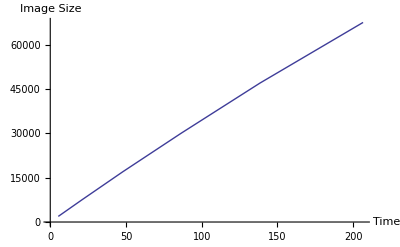

```mathematica
ListLinePlot[dataDES,AxesLabel->{"Time","Image Size"}]
```

◀     |     ▶

## concluding remarks

The restored image matches the plain-image only when the initial condition of the CNN decryption signal, the DES-key, the control coefficients and the internal precision are all correct.

The restored image is extremely sensitive to changes in both the internal precision and the initial condition of the CNN decryption signal.

The image restored from an imperfectly transmitted cipher-image may still be desirable, and even more so as the bit corruption clustering increases.

This hybrid algorithm is not only a remedy for the small key space of DES, but also resists the attacks on chaotic encryption systems by determining initial conditions outlined in [11] and [12].

The time complexity is a serious issue at this stage.

The resistance of the algorithm to linear and differential cryptanalysis is under investigation.

The scheme is also suitable for encryption of text, audio and video.

◀     |     ▶

## the Data Encryption Standard

The secure communication scheme already presented essentially treats the functions DESEncrypt and DESDecrypt as black-boxes which encrypt and decrypt, respectively, a block of 64-bits, in accordance with [5].

```mathematica
Off[General::spell,General::spell1]
Needs["Graphics`Colors`"]
Needs["LinearAlgebra`MatrixManipulation`"]
```

### E-box

```mathematica
Expansion::"BitLength"="Expansion requires its argument to have a bit length of `1`. You supplied an argument of bit length `2`.";
```

```mathematica
Expansion[x_Integer]:=Expansion[IntegerDigits[x,2,32]]
```

```mathematica
Expansion[bits_?VectorQ]:=Module[{len},len=Length[bits];If[32!=len,Message[Expansion::"BitLength",32,len],bits[[{32,1,2,3,4,5,4,5,6,7,8,9,8,9,10,11,12,13,12,13,14,15,16,17,16,17,18,19,20,21,20,21,22,23,24,25,24,25,26,27,28,29,28,29,30,31,32,1}]]]]
```

### S-boxes

```mathematica
s1={{14,4,13,1,2,15,11,8,3,10,6,12,5,9,0,7},{0,15,7,4,14,2,13,1,10,6,12,11,9,5,3,8},{4,1,14,8,13,6,2,11,15,12,9,7,3,10,5,0},{15,12,8,2,4,9,1,7,5,11,3,14,10,0,6,13}};
```

```mathematica
s2={{15,1,8,14,6,11,3,4,9,7,2,13,12,0,5,10},{3,13,4,7,15,2,8,14,12,0,1,10,6,9,11,5},{0,14,7,11,10,4,13,1,5,8,12,6,9,3,2,15},{13,8,10,1,3,15,4,2,11,6,7,12,0,5,14,9}};
```

```mathematica
s3={{10,0,9,14,6,3,15,5,1,13,12,7,11,4,2,8},{13,7,0,9,3,4,6,10,2,8,5,14,12,11,15,1},{13,6,4,9,8,15,3,0,11,1,2,12,5,10,14,7},{1,10,13,0,6,9,8,7,4,15,14,3,11,5,2,12}};
```

```mathematica
s4={{7,13,14,3,0,6,9,10,1,2,8,5,11,12,4,15},{13,8,11,5,6,15,0,3,4,7,2,12,1,10,14,9},{10,6,9,0,12,11,7,13,15,1,3,14,5,2,8,4},{3,15,0,6,10,1,13,8,9,4,5,11,12,7,2,14}};
```

```mathematica
s5={{2,12,4,1,7,10,11,6,8,5,3,15,13,0,14,9},{14,11,2,12,4,7,13,1,5,0,15,10,3,9,8,6},{4,2,1,11,10,13,7,8,15,9,12,5,6,3,0,14},{11,8,12,7,1,14,2,13,6,15,0,9,10,4,5,3}};
```

```mathematica
s6={{12,1,10,15,9,2,6,8,0,13,3,4,14,7,5,11},{10,15,4,2,7,12,9,5,6,1,13,14,0,11,3,8},{9,14,15,5,2,8,12,3,7,0,4,10,1,13,11,6},{4,3,2,12,9,5,15,10,11,14,1,7,6,0,8,13}};
```

```mathematica
s7={{4,11,2,14,15,0,8,13,3,12,9,7,5,10,6,1},{13,0,11,7,4,9,1,10,14,3,5,12,2,15,8,6},{1,4,11,13,12,3,7,14,10,15,6,8,0,5,9,2},{6,11,13,8,1,4,10,7,9,5,0,15,14,2,3,12}};
```

```mathematica
s8={{13,2,8,4,6,15,11,1,10,9,3,14,5,0,12,7},{1,15,13,8,10,3,7,4,12,5,6,11,0,14,9,2},{7,11,4,1,9,12,14,2,0,6,10,13,15,3,5,8},{2,1,14,7,4,10,8,13,15,12,9,0,3,5,6,11}};
```

```mathematica
SBox[s_?MatrixQ,z_?VectorQ]:=Module[{row,column},row=1+FromDigits[Drop[z,{2,5}],2];column=1+FromDigits[Take[z,{2,5}],2];s[[row,column]]]
```

```mathematica
ApplySBoxes[z_?MatrixQ]:=Module[{tmp},tmp=Transpose[{{s1,s2,s3,s4,s5,s6,s7,s8},z}];tmp=Apply[SBox,tmp,{1}];Map[IntegerDigits[#,2,4]&,tmp]]
```

### P-box

```mathematica
FP::"BitLength"="FP requires its argument to have a bit length of `1`. You supplied an argument of bit length `2`.";
```

```mathematica
FP[c_Integer]:=FP[IntegerDigits[c,2,32]]
```

```mathematica
FP[bits_?VectorQ]:=Module[{len},len=Length[bits];If[32!=len,Message[FP::"BitLength",32,len],bits[[{16,7,20,21,29,12,28,17,1,15,23,26,5,18,31,10,2,8,24,14,32,27,3,9,19,13,30,6,22,11,4,25}]]]]
```

### Feistel function

```mathematica
f::"xBitLength"="The DES function requires its first argument to have a bit length of `1`. You supplied an argument of bit length `2`.";
```

```mathematica
f::"yBitLength"="The DES function requires its second argument to have a bit length of `1`. You supplied an argument of bit length `2`.";
```

```mathematica
f[x_Integer,y_Integer]:=f[IntegerDigits[x,2,32],IntegerDigits[y,2,48]]
```

```mathematica
f[xbits_?VectorQ,y_Integer]:=f[xbits,IntegerDigits[y,2,48]]
```

```mathematica
f[x_Integer,ybits_?VectorQ]:=f[IntegerDigits[x,2,32],ybits]
```

```mathematica
f[xbits_?VectorQ,ybits_?VectorQ]:=Module[{tmp,len},len=Length[xbits];If[32!=len,Message[f::"xBitLength",32,len];Return[]];len=Length[ybits];If[48!=len,Message[f::"yBitLength",48,len];Return[]];tmp=Mod[Expansion[xbits]+ybits,2];tmp=Partition[tmp,6];tmp=ApplySBoxes[tmp];FP[Flatten[tmp]]]
```

### key schedule

```mathematica
PC1::"BitLength"="PC1 requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
PC1[bits_?VectorQ]:=Module[{len},len=Length[bits];If[64!=len,Message[PC1::"BitsLength",64,len],bits[[{57,49,41,33,25,17,9,1,58,50,42,34,26,18,10,2,59,51,43,35,27,19,11,3,60,52,44,36,63,55,47,39,31,23,15,7,62,54,46,38,30,22,14,6,61,53,45,37,29,21,13,5,28,20,12,4}]]]]
```

```mathematica
PC1[k_Integer]:=PC1[IntegerDigits[k,2,64]]
```

```mathematica
PC2::"BitLength"="PC2 requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
PC2[bits_?VectorQ]:=Module[{len},len=Length[bits];If[56!=len,Message[PC2::"BitLength",56,len],bits[[{14,17,11,24,1,5,3,28,15,6,21,10,23,19,12,4,26,8,16,7,27,20,13,2,41,52,31,37,47,55,30,40,51,45,33,48,44,49,39,56,34,53,46,42,50,36,29,32}]]]]
```

```mathematica
PC2[k_Integer]:=PC2[IntegerDigits[k,2,56]]
```

```mathematica
KeyShift::"KeyLength"="KeyShift requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
KeyShift[key_?VectorQ,round_Integer,opts___Rule]:=Module[{left,right,len},len=Length[key];If[56!=len,Message[KeyShift::"KeyLength",56,len];Return[]];left=Take[key,28];right=Take[key,-28];If[MemberQ[{1,2,9,16},round],Join[RotateLeft[left],RotateLeft[right]],Join[RotateLeft[left,2],RotateLeft[right,2]]]]
```

```mathematica
KeyShift[key_Integer,round_Integer]:=KeyShift[IntegerDigits[key,2,56],round]
```

### initial permutation

```mathematica
IP::"BitLength"="IP requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
IPInv::"BitLength"="IPInv requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
IP[x_Integer]:=IP[IntegerDigits[x,2,64]]
```

```mathematica
IP[bits_?VectorQ]:=Module[{len},len=Length[bits];If[64!=len,Message[IP::"BitLength",64,len],bits[[{58,50,42,34,26,18,10,2,60,52,44,36,28,20,12,4,62,54,46,38,30,22,14,6,64,56,48,40,32,24,16,8,57,49,41,33,25,17,9,1,59,51,43,35,27,19,11,3,61,53,45,37,29,21,13,5,63,55,47,39,31,23,15,7}]]]]
```

```mathematica
IPInv[x_Integer]:=IPInv[IntegerDigits[x,2,64]]
```

```mathematica
IPInv[bits_?VectorQ]:=Module[{len},len=Length[bits];If[64!=len,Message[IPInv::"BitLength",64,len],bits[[{40,8,48,16,56,24,64,32,39,7,47,15,55,23,63,31,38,6,46,14,54,22,62,30,37,5,45,13,53,21,61,29,36,4,44,12,52,20,60,28,35,3,43,11,51,19,59,27,34,2,42,10,50,18,58,26,33,1,41,9,49,17,57,25}]]]]
```

### rounds

```mathematica
DESRound::"BitLength"="DESRound requires a bit string of `1` bits. The supplied bit string contained only `2` bits.";
```

```mathematica
DESRound::"KeyLength"="DESRound requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
DESRound[bits_?VectorQ,key_?VectorQ]:=Module[{len,left,right},len=Length[bits];If[64!=len,Message[DESRound::"BitLength",64,len];Return[]];len=Length[key];If[48!=len,Message[DESRound::"KeyLength",48,len];Return[]];left=Take[bits,32];right=Take[bits,-32];Join[right,Mod[left+f[right,key],2]]]
```

```mathematica
DESRound[x_Integer,key_?VectorQ]:=DESRound[IntegerDigits[x,2,64],key]
```

```mathematica
DESRound[bits_?VectorQ,key_Integer]:=DESRound[bits,IntegerDigits[key,2,48]]
```

```mathematica
DESRound[x_Integer,key_Integer]:=DESRound[IntegerDigits[x,2,64],IntegerDigits[key,2,48]]
```

```mathematica
DESEncrypt::"KeyLength"="DESEncrypt requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
DESEncrypt::"TextLength"="DESEncrypt requires a plaintext bit string of `1` bits. The supplied plaintext bit string contained only `2` bits.";
```

```mathematica
Options[DESEncrypt]={Verbose->False,Base->16};
```

```mathematica
DESEncrypt[plaintext_?VectorQ,key_?VectorQ,opts___Rule]:=Module[{len,verbosity,pt,keyn,base},len=Length[plaintext];If[64!=len,Message[DESEncrypt::"TextLength",64,len];Return[]];len=Length[key];If[64!=len,Message[DESEncrypt::"KeyLength",64,len];Return[]];verbosity=Verbose/.{opts}/.Options[DESEncrypt];base=Base/.{opts}/.Options[DESEncrypt];pt=IP[plaintext];keyn=PC1[key];If[verbosity,Print["Plaintext: ",BaseForm[FromDigits[plaintext,2],base],", Initial Permutation: ",BaseForm[FromDigits[pt,2],base]]];Do[keyn=KeyShift[keyn,j];pt=DESRound[pt,PC2[keyn]];If[verbosity,Print["DES Encryption Round ",j,".\nkey = ",BaseForm[FromDigits[PC2[keyn],2],base],", bit string = ",BaseForm[FromDigits[pt,2],base]]],{j,1,16,1}];pt=Join[Take[pt,-32],Take[pt,32]];IPInv[pt]]
```

```mathematica
DESEncrypt[plaintext_Integer,key_?VectorQ,opts___Rule]:=DESEncrypt[IntegerDigits[plaintext,2,64],key,opts]
```

```mathematica
DESEncrypt[plaintext_?VectorQ,key_Integer,opts___Rule]:=DESEncrypt[plaintext,IntegerDigits[key,2,64],opts]
```

```mathematica
DESEncrypt[plaintext_Integer,key_Integer,opts___Rule]:=DESEncrypt[IntegerDigits[plaintext,2,64],IntegerDigits[key,2,64],opts]
```

```mathematica
DESDecrypt::"KeyLength"="DESDecrypt requires a key of `1` bits. The supplied key contained only `2` bits.";
```

```mathematica
DESDecrypt::"TextLength"="DESDecrypt requires a ciphertext bit string of `1` bits. The supplied ciphertext bit string contained only `2` bits.";
```

```mathematica
DESDecrypt[ciphertext_?VectorQ,key_?VectorQ,opts___Rule]:=Module[{len,verbosity,pt,keyc,keys,base},len=Length[ciphertext];If[64!=len,Message[DESDecrypt::"TextLength",64,len];Return[]];len=Length[key];If[64!=len,Message[DESDecrypt::"KeyLength",64,len];Return[]];verbosity=Verbose/.{opts}/.Options[DESEncrypt];base=Base/.{opts}/.Options[DESEncrypt];pt=IP[ciphertext];keys={};keyc=PC1[key];Do[keyc=KeyShift[keyc,j];keys=Prepend[keys,PC2[keyc]],{j,1,16,1}];Do[pt=DESRound[pt,keys[[j]]];If[verbosity,Print["DES Decryption Round ",j,".\nkey = ",BaseForm[FromDigits[keys[[j]],2],base],", bit string = ",BaseForm[FromDigits[pt,2],base]]],{j,1,16,1}];pt=Join[Take[pt,-32],Take[pt,32]];IPInv[pt]]
```

```mathematica
DESDecrypt[plaintext_Integer,key_?VectorQ,opts___Rule]:=DESDecrypt[IntegerDigits[plaintext,2,64],key,opts]
```

```mathematica
DESDecrypt[plaintext_?VectorQ,key_Integer,opts___Rule]:=DESDecrypt[plaintext,IntegerDigits[key,2,64],opts]
```

```mathematica
DESDecrypt[plaintext_Integer,key_Integer,opts___Rule]:=DESDecrypt[IntegerDigits[plaintext,2,64],IntegerDigits[key,2,64],opts]
```

◀     |     ▶

## acknowledgements

A. S. is grateful to Dr. S. K. Dana for motivating this project. He also thanks Mr. Manojit Chattopadhyay, and all his teachers at the Pailan College of Management & Technology for their patience and encouragement, and his parents for their constant support and assistance.

◀     |     ▶

## bibliography and references

Ott, Chaos in Dynamical Systems, 2nd ed., Cambridge University Press, 2002.

Ruskeepaa, Mathematica Navigator: Mathematics, Statistics and Graphics, 3rd ed., Academic Press, 2009.

Schneier, Applied Cryptography: Protocols, Algorithms, and Source Code in C, 2nd ed., Wiley, 1996.

Yalcin, Suykens and Vandewalle, Cellular Neural Networks, Multi-Scroll Chaos and Synchronization, World Scientific Series on Nonlinear Science, A 50, 2005.

Federal Information Processing Standards, Data Encryption Standard (DES), FIPS PUB 46-3, U.S. Department of Commerce/NIST, 1999.

Chua and Yang, “Cellular Neural Networks: Theory,” IEEE Transactions on Circuits and Systems, 35(10), pp. 1257–1272, 1988.

Zhang, Peng, Yang and Wei, “A Digital Image Encryption Scheme Based on the Hybrid of Cellular Neural Network and Logistic Map,” ISSN 2005, LNCS 3497, pp. 860-867, 2005.

Baptista, “Cryptography with Chaos,” Physics Letters, A 240, no. 1-2, 50-4, 1998.

Zhenya, Yifeng and Hongtao, “The Dynamic Character of Cellular Neural Network with Applications to Secure Communication,” Journal of China Institute of Communications, 20(3), pp. 59-67, 1999.

Shuisheng, Yanfeng, Min et al., “Discussion on Chaotic Secure Communication and New Schemes of Chaotic Encryption,” Journal of South China University of Technology (Natural Science Edition), 30(11), pp. 75-80, 2002.

Sobhy and Shehata, “Methods of Attacking Chaotic Encryption and Countermeasures,” IEEE International Conference on ASSP, 2, pp. 1001-1004, 2001.

Kapoor, “Chaos and Cryptography”, 2003.

Roskin and Casper, “From Chaos to Cryptography”.

Cristea, Cehan and Grecu, “Applications of Chaos Theory in Cryptography”.

Bose and Banerjee, “Implementing Symmetric Cryptography Using Chaos Functions”.

◀     |     ▶